```mathematica
ineqs=Table[allGraphs[k,"comp"][allGraphs[k,"colofourrealnull"],0],{k,Keys[allGraphs]}];Length[ineqs]
```

15

```mathematica
countDone=0;MyLeafCount[exp_]:=Block[{},countDone++;StringLength[ToString[exp]]]
```

```mathematica
ineqsW=Monitor[Simplify[Fold[And,ineqs],Trig->False,ComplexityFunction->MyLeafCount,Assumptions->nullAtomFacts],countDone];Length[ineqsW]
```

15

```mathematica
Length[ineqsW]
```

15

```mathematica
vars=ListofVars[Select[ineqsW,Length[ListofVars[#]]==2&]]
```

{n123,n12x3,n123,n13x2,n123,n1x23,n12x3,n1x2x3,n13x2,n1x2x3,n1x23,n1x2x3}

```mathematica
ineqs2=Table[allGraphs[k,"comp"][allGraphs[k,"colofourrealnull"],0],{k,Keys[allGraphs]}];Length[ineqs]
```

15

```mathematica
ineqs2
```

{n1x2x3>0,-n12x3+n1x2x3>0,n123-n12x3-n13x2+n1x2x3>0,2 n123-n12x3-n13x2-n1x23+n1x2x3>0,-n123+n1x23>0,-n123+n13x2>0,n123-n12x3-n1x23+n1x2x3>0,n12x3>0,-n123+n12x3>0,n123>0,-n13x2+n1x2x3>0,n123-n13x2-n1x23+n1x2x3>0,n13x2>0,-n1x23+n1x2x3>0,n1x23>0}

```mathematica
realnullAtomFacts=Table[allGraphs[k]["comp"][allGraphs[k]["colofourrealnull"],0],{k,realyNullAtomKeys}];Length[realnullAtomFacts]
```

5

```mathematica
ineqsW2=Monitor[Simplify[Fold[And,ineqs2],Trig->False,ComplexityFunction->MyLeafCount],countDone];Length[ineqsW2]
```

15

```mathematica
Length[allGraphs]
```

15

```mathematica
Table[Labeled[allGraphs[k,"graph"],{ChromaticPolynomial[allGraphs[k,"graph"],x],TableForm[{k,allGraphs[k,"colofourrealnull"],allGraphs[k,"colofournull"],allGraphs[k,"colofour"]}]},{Top,Bottom}],{k,Keys[allGraphs]}]
```

{-Graphics-x^30
n1x2x3
p1x2x3
v123+v12x3+v13x2+v1x23+v1x2x3,-Graphics--x^2+x^39
-n12x3+n1x2x3
p12x3
v13x2+v1x23+v1x2x3,-Graphics-x-2 x^2+x^312
n123-n12x3-n13x2+n1x2x3
1/2 (p123+p12x3+p13x2-p1x23)
v1x23+v1x2x3,-Graphics-2 x-3 x^2+x^313
2 n123-n12x3-n13x2-n1x23+n1x2x3
p123
v1x2x3,-Graphics--x+x^214
-n123+n1x23
1/2 (-p123+p12x3+p13x2-p1x23)
v1x23,-Graphics--x+x^216
-n123+n13x2
1/2 (-p123+p12x3-p13x2+p1x23)
v13x2,-Graphics-x-2 x^2+x^310
n123-n12x3-n1x23+n1x2x3
1/2 (p123+p12x3-p13x2+p1x23)
v13x2+v1x2x3,-Graphics-x^218
n12x3
-p12x3+p1x2x3
v123+v12x3,-Graphics--x+x^222
-n123+n12x3
1/2 (-p123-p12x3+p13x2+p1x23)
v12x3,-Graphics-x26
n123
1/2 (p123-p12x3-p13x2-p1x23+2 p1x2x3)
v123,-Graphics--x^2+x^33
-n13x2+n1x2x3
p13x2
v12x3+v1x23+v1x2x3,-Graphics-x-2 x^2+x^34
n123-n13x2-n1x23+n1x2x3
1/2 (p123-p12x3+p13x2+p1x23)
v12x3+v1x2x3,-Graphics-x^26
n13x2
-p13x2+p1x2x3
v123+v13x2,-Graphics--x^2+x^31
-n1x23+n1x2x3
p1x23
v12x3+v13x2+v1x2x3,-Graphics-x^22
n1x23
-p1x23+p1x2x3
v123+v1x23}

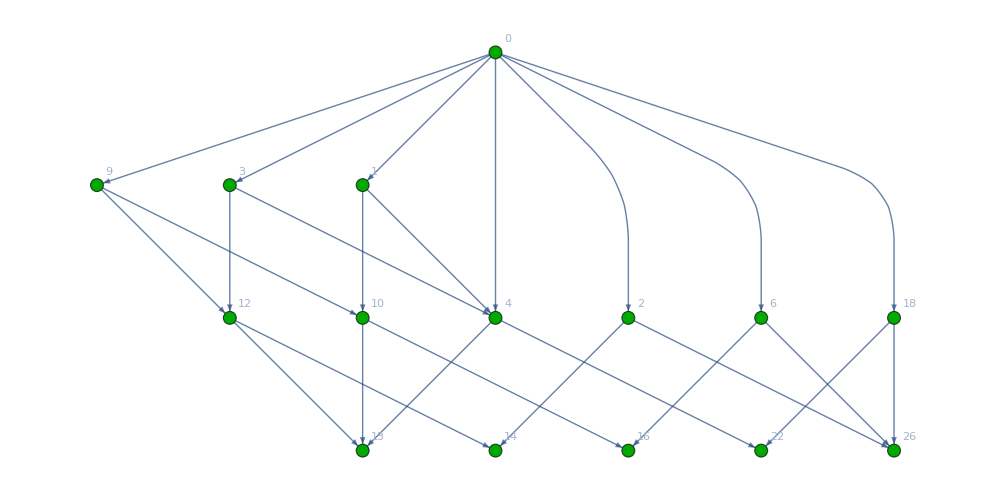

```mathematica
partialOrder=Graph[{0->9,0->18,0->3,0->4,0->6,0->1,0->2 (*0->14,0->13,0->16,0->26,0->22,0->10,0->12*),
(*9->16,9->14,9->13,*)
12->14,12->13,
10->16,10->13,
18->26,18->22,
(*3->22,3->14,3->13,*)
4->22,4->13,
6->26,6->16,
(*1->22,1->16,1->13,*)
2->26,2->14,
3->4,3->12,
1->10,1->4,
9->10,9->12},VertexLabels->Table[g->Labeled[allGraphs[g,"graph"],Style[g,Blue]],{g,Keys[allGraphs]}],GraphLayout->"LayeredDigraphEmbedding", VertexStyle->Table[g->ColourForKey[allGraphs,g],{g,Keys[allGraphs]}]]
```

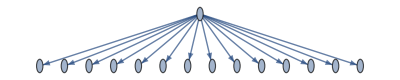

```mathematica
FindSpanningTree[partialOrder]
```

```mathematica
allGraphs[9,"colofourrealnull"]
```

-n12x3+n1x2x3

```mathematica
vars2=ListofVars[Select[ineqsW2,Length[ListofVars[#]]==2&]]
```

{n123,n12x3,n123,n13x2,n123,n1x23,n12x3,n1x2x3,n13x2,n1x2x3,n1x23,n1x2x3}

```mathematica
partialOrder=Graph[Join[{0->9,0->3,0->1,  9->14,9->16,9->22,36->12,36->16,36->13,18->26,18->22,3->22,3->14,3->13,4->22,4->13,6->26,6->16,1->22,1->16,1->13,2->26,2->14},Map[InverseNull[#[[1]]]->InverseNull[#[[2]]]&,AndToTable[Select[ineqsW2,Length[ListofVars[#]]==2&]]]],VertexLabels->Table[g->Labeled[allGraphs[g,"graph"],TableForm[{allGraphs[g,"colofourrealnull"],allGraphs[g,"colofournull"],allGraphs[g,"colofour"]}],{Bottom,Top}],{g,Keys[allGraphs]}],GraphLayout->"LayeredDigraphEmbedding", VertexStyle->Table[g->ColourForKey[allGraphs,g],{g,Keys[allGraphs]}]]
```

Graph[{0→9,0→3,0→1,9→14,9→16,9→22,36→12,36→16,36→13,18→26,18→22,3→22,3→14,3→13,4→22,4→13,6→26,6→16,1→22,1→16,1→13,2→26,2→14,0→18,2→26,6→26,18→26,0→6,0→2},VertexLabels→{0→-Graphics-n1x2x3
p1x2x3
v123+v12x3+v13x2+v1x23+v1x2x3,9→-Graphics--n12x3+n1x2x3
p12x3
v13x2+v1x23+v1x2x3,12→-Graphics-n123-n12x3-n13x2+n1x2x3
1/2 (p123+p12x3+p13x2-p1x23)
v1x23+v1x2x3,13→-Graphics-2 n123-n12x3-n13x2-n1x23+n1x2x3
p123
v1x2x3,14→-Graphics--n123+n1x23
1/2 (-p123+p12x3+p13x2-p1x23)
v1x23,16→-Graphics--n123+n13x2
1/2 (-p123+p12x3-p13x2+p1x23)
v13x2,10→-Graphics-n123-n12x3-n1x23+n1x2x3
1/2 (p123+p12x3-p13x2+p1x23)
v13x2+v1x2x3,18→-Graphics-n12x3
-p12x3+p1x2x3
v123+v12x3,22→-Graphics--n123+n12x3
1/2 (-p123-p12x3+p13x2+p1x23)
v12x3,26→-Graphics-n123
1/2 (p123-p12x3-p13x2-p1x23+2 p1x2x3)
v123,3→-Graphics--n13x2+n1x2x3
p13x2
v12x3+v1x23+v1x2x3,4→-Graphics-n123-n13x2-n1x23+n1x2x3
1/2 (p123-p12x3+p13x2+p1x23)
v12x3+v1x2x3,6→-Graphics-n13x2
-p13x2+p1x2x3
v123+v13x2,1→-Graphics--n1x23+n1x2x3
p1x23
v12x3+v13x2+v1x2x3,2→-Graphics-n1x23
-p1x23+p1x2x3
v123+v1x23},GraphLayout→LayeredDigraphEmbedding,VertexStyle→{0→RGBColor[0, Rational[2, 3], 0],9→RGBColor[0, Rational[2, 3], 0],12→RGBColor[0, Rational[2, 3], 0],13→RGBColor[0, Rational[2, 3], 0],14→RGBColor[0, Rational[2, 3], 0],16→RGBColor[0, Rational[2, 3], 0],10→RGBColor[0, Rational[2, 3], 0],18→RGBColor[0, Rational[2, 3], 0],22→RGBColor[0, Rational[2, 3], 0],26→RGBColor[0, Rational[2, 3], 0],3→RGBColor[0, Rational[2, 3], 0],4→RGBColor[0, Rational[2, 3], 0],6→RGBColor[0, Rational[2, 3], 0],1→RGBColor[0, Rational[2, 3], 0],2→RGBColor[0, Rational[2, 3], 0]}]

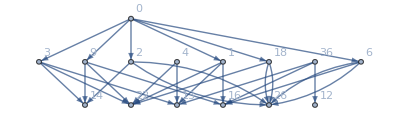

```mathematica
Graph[{0->9,0->3,0->1,9->14,9->16,9->22,36->12,36->16,36->13,18->26,18->22,3->22,3->14,3->13,4->22,4->13,6->26,6->16,1->22,1->16,1->13,2->26,2->14,0->18,2->26,6->26,18->26,0->6,0->2},VertexLabels->"Name"]
```

```mathematica
InverseNull[symbol_]:=First[Select[Keys[allGraphs],allGraphs[#,"colofourrealnull"]==symbol&]]
```

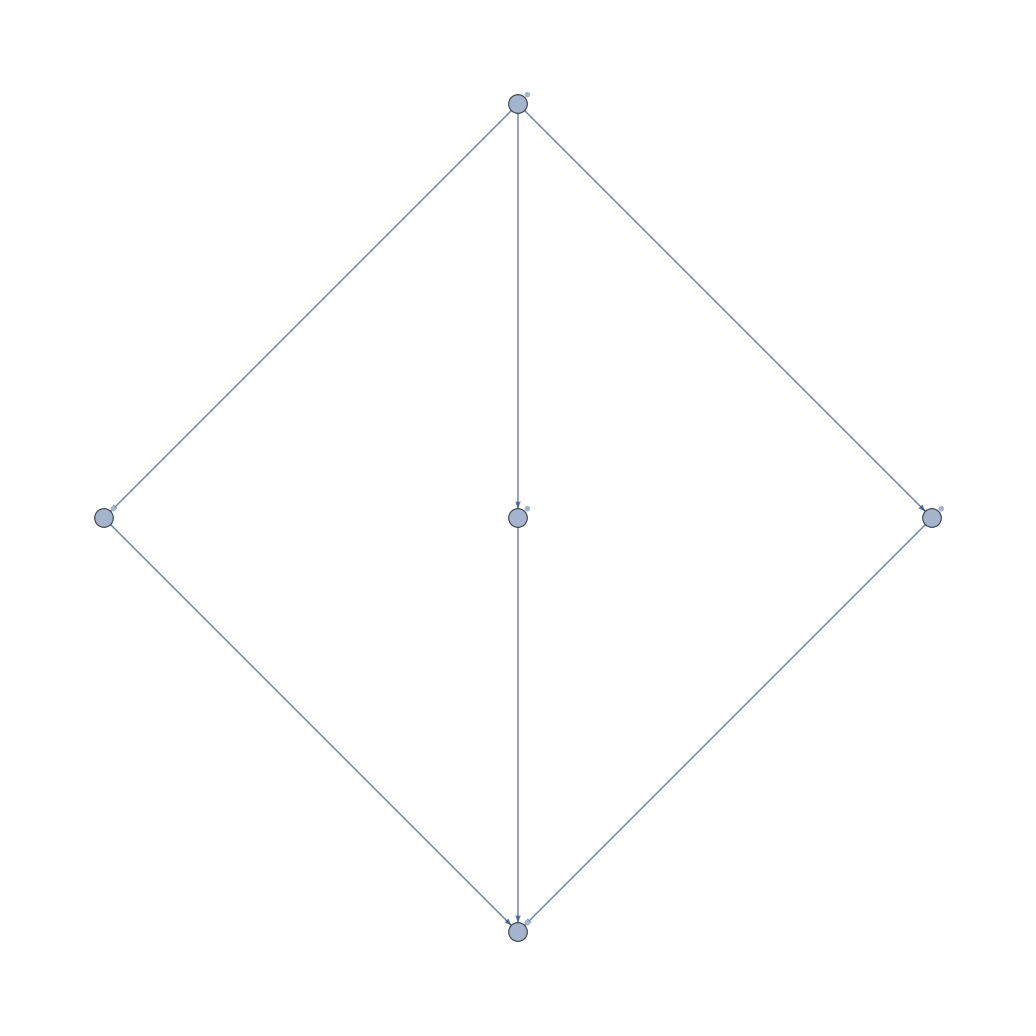

```mathematica
Graph[Map[#[[1]]->#[[2]]&,AndToTable[Select[ineqsW2,Length[ListofVars[#]]==2&]]],VertexLabels->Select[Table[allGraphs[k,"colofourrealnull"]->allGraphs[k,"graph"],{k,realyNullAtomKeys}],MemberQ[vars2,#[[1]]]&]]
```

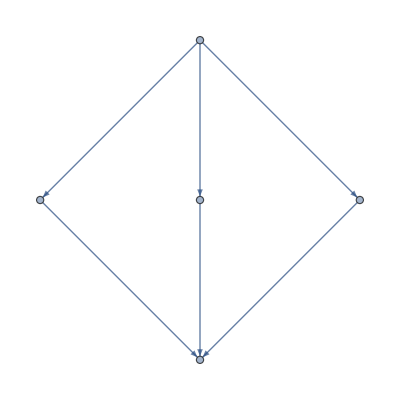

```mathematica
Graph[Map[#[[1]]->#[[2]]&,AndToTable[Select[ineqsW,Length[ListofVars[#]]==2&]]],VertexLabels->Select[Table[allGraphs[k,"colofournull"]->allGraphs[k,"graph"],{k,nullAtomKeys}],MemberQ[vars,#[[1]]]&]]
```

```mathematica
Take[ineqsW,5]
```

n1x2x3>0&&n1x2x3>n12x3&&n123+n1x2x3>n12x3+n13x2&&2 n123+n1x2x3>n12x3+n13x2+n1x23&&n1x23>n123

```mathematica
pairs=Subsets[nullAtomSymbols,{2}];Length[pairs]
```

10

```mathematica
Take[nullAtomFacts,3]
```

{p1x2x3>0,p1x23>0,p13x2>0}

```mathematica
atomFactsAnd=Fold[And,nullAtomFacts]
```

p1x2x3>0&&p1x23>0&&p13x2>0&&p12x3>0&&p123>0

```mathematica
Monitor[Table[{p[[1]]<p[[2]]}->Length[Simplify[p[[1]]>p[[2]]&&atomFactsAnd,Trig->False,ComplexityFunction->MyLeafCount,Assumptions->nullAtomFacts]],{p,pairs}],Position[pairs, p]]
```

{{p1x2x3<p1x23}→2,{p1x2x3<p13x2}→2,{p1x2x3<p12x3}→2,{p1x2x3<p123}→2,{p1x23<p13x2}→2,{p1x23<p12x3}→2,{p1x23<p123}→2,{p13x2<p12x3}→2,{p13x2<p123}→2,{p12x3<p123}→2}

```mathematica
Select[nullAtomSymbols,!MemberQ[ListofVars[ Table[allGraphs[k,"colofournull"],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]//Total//Expand],#]&]
```

{p1x2x3,p1x23,p13x2,p12x3,p123}

```mathematica
Select[Keys[allGraphs],allGraphs[#,"colofournull"]==p1x2x3x4x5&]
```

{}

```mathematica
allGraphs[0,"graph"]
```

-Graphics-

```mathematica
allGraphs[quad1Key,"colofournull"]/.repcolofournullgraph2//Expand//Length
```

2

```mathematica
Select[nullAtomSymbols,!MemberQ[ListofVars[ Table[allGraphs[k,"colofournull"],{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]//Total//Expand],#]&]
```

{p1x2x3,p1x23,p13x2,p12x3,p123}

```mathematica
Select[Keys[allGraphs],MemberQ[{p1x2x3x4x5,p1x25x34,p15x24x3,p14x23x5,p13x2x45,p12x35x4},allGraphs[#,"colofournull"]]&]
```

{}

```mathematica
allGraphs[6562,"graph"]
```

Missing[KeyAbsent,6562]